```mathematica
(*3d embedding with Kirchhoff-love of pringle*)X[r_, ϕ_, s_] = FullSimplify[RotationMatrix[θ, {0,0,1}].(c{r Cos[θ + α+ ϕ]-r^3 Cos[θ+α + 3ϕ]/(3R^2), -r Sin[θ+α+ ϕ]-r^3 Sin[θ+α + 3ϕ]/(3R^2), r^2/R Cos[θ+α + 2ϕ]} + s {(2 r R Cos[ϕ + θ])/(r^2+R^2),(2 r R Sin[ϕ + θ])/(r^2+R^2),(r^4-R^4)/((r^2+R^2)^2)})];
```

```mathematica
(*Dimensionless Cylindrical coordinates*)
u = FullSimplify[(X[R, ϕ, h/2]-(X[R, ϕ, h/2]/.θ->0)).{0,1,0}/R - d/R]
ρ = FullSimplify[Sqrt[(X[R, ϕ, h/2].{1,0,0})^2+(X[R, ϕ, h/2].{0,0,1})^2]/R]
```

(-3 d+3 h Cos[θ+ϕ] Sin[θ]-2 c R Cos[α+θ+3 ϕ] Sin[θ])/(3 R)

(√(c^2 R^2 Cos[α+θ+2 ϕ]^2+(c R Cos[α+ϕ]+1/2 h Cos[2 θ+ϕ]-1/3 c R Cos[α+2 θ+3 ϕ])^2))/R

```mathematica
(*Radial unit vector*)
erho = {1,0,0}FullSimplify[(X[R, ϕ, h/2].{1,0,0})/(R ρ)] + {0,0,1}FullSimplify[(X[R, ϕ, h/2].{0,0,1})/(R ρ)]
```

{(c R Cos[α+ϕ]+1/2 h Cos[2 θ+ϕ]-1/3 c R Cos[α+2 θ+3 ϕ])/(√(c^2 R^2 Cos[α+θ+2 ϕ]^2+(c R Cos[α+ϕ]+1/2 h Cos[2 θ+ϕ]-1/3 c R Cos[α+2 θ+3 ϕ])^2)),0,(c R Cos[α+θ+2 ϕ])/(√(c^2 R^2 Cos[α+θ+2 ϕ]^2+(c R Cos[α+ϕ]+1/2 h Cos[2 θ+ϕ]-1/3 c R Cos[α+2 θ+3 ϕ])^2))}

```mathematica
(*Force from the magnetic interaction*)
F[θ_, ϕ_, α_,d_]= D[({(2 r R Cos[ϕ+θ])/(r^2+R^2),(2 r R Sin[ϕ+θ])/(r^2+R^2),(r^4-R^4)/((r^2+R^2)^2)}/. {r->R}).(u erho - ρ{0,1,0})/(u^2 + ρ^2)^(3/2), θ];
```

```mathematica
FullSimplify[Series[F[θ,0, 0, d], {θ, 0,1}]]
```

(-77911.8-324.579 d^2)/((70.8245+1. d^2)^(5/2))+((2.0696×10^6 d+6954.42 d^3-59.4586 d^5) θ)/((70.8245+1. d^2)^(7/2))+O[θ]^2

## Nonlinear numerical solutions

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T, eq]
eq = θ''[t] + A  θ'[t]+ Sin[θ[t]] - B Cos[(ω/ω0) t]F[θ[t],ϕ, α, d];
```

Modes transitioning from smooth rotations to complex rotations as a function of frequency at short distances

{{θ[t]→InterpolatingFunction[…][t]}}

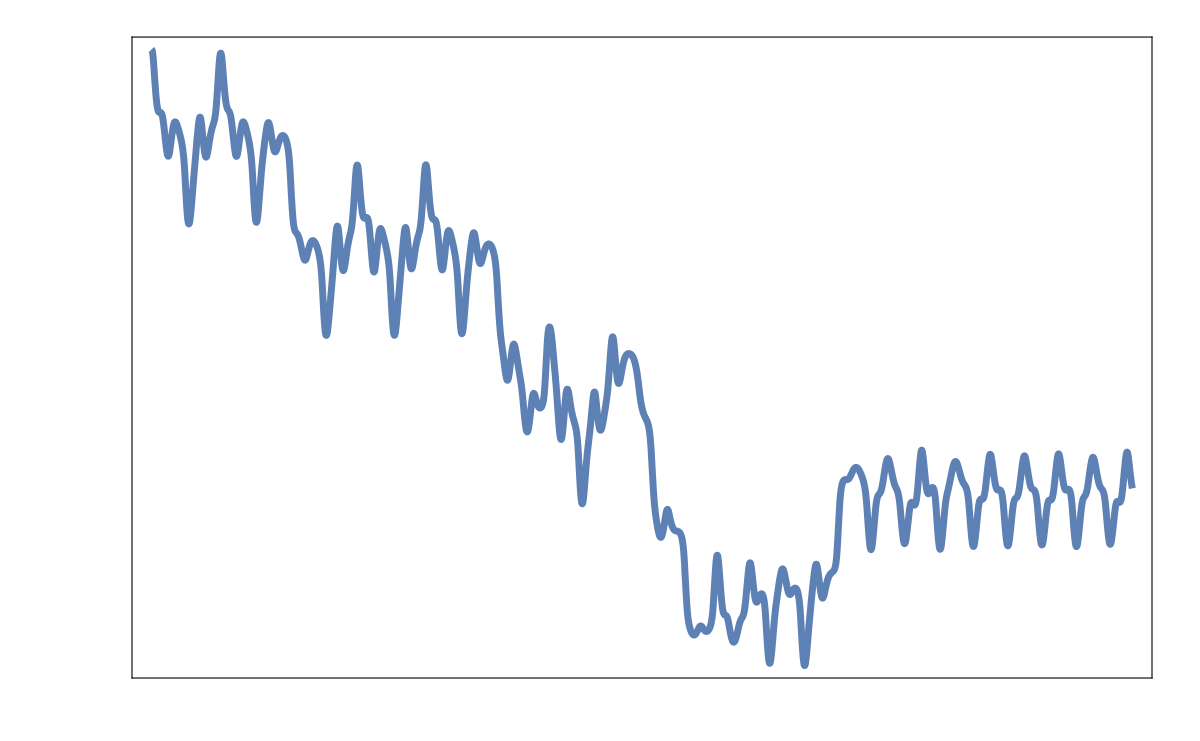

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.05;
T = 200;
ω = 4.5;
sol1 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
FigPlot1 = Plot[(θ[t]/. sol1)/2, {t, 0, T},PlotRange->All,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-20,0,5}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["545Bonnet.svg", FigPlot1]
```

545Bonnet.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega45d05.csv", data]
```

omega45d05.csv

{{θ[t]→InterpolatingFunction[…][t]}}

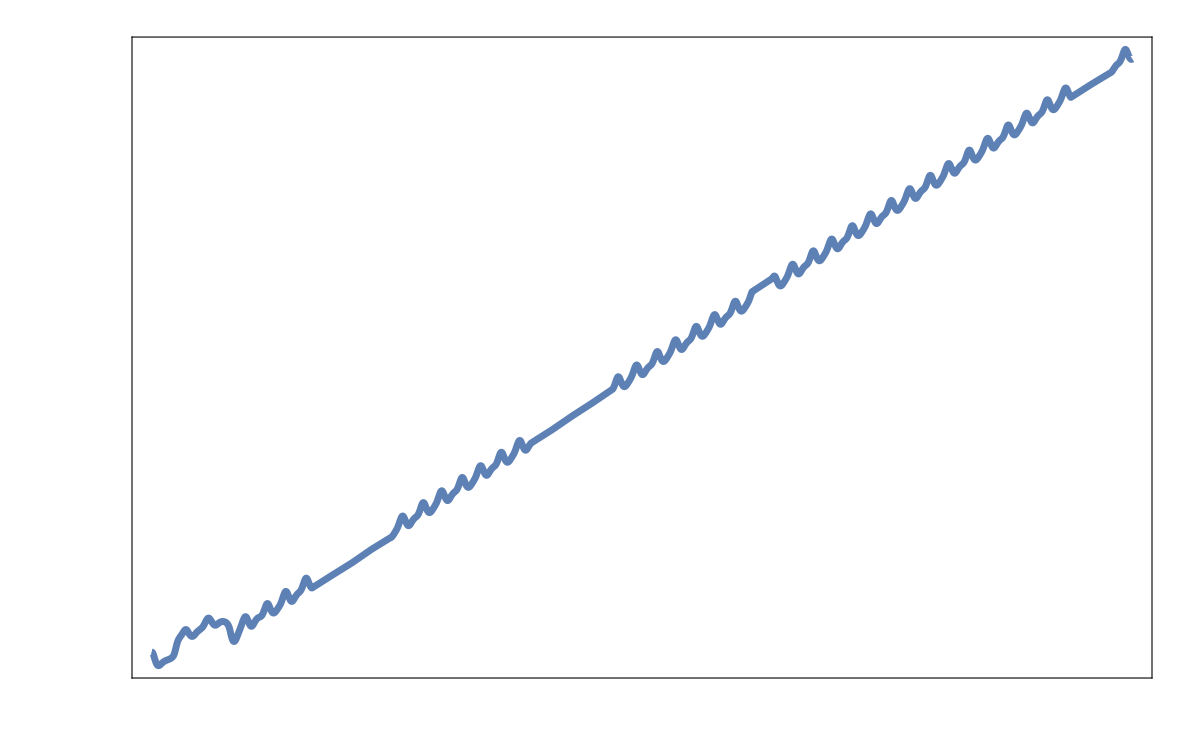

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.05;
T = 200;
ω = 3.95;
sol2 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
FigPlot2 = Plot[(θ[t]/. sol2)/2, {t, 0, T},PlotRange->All,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,0,60,20}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["5395Bonnet.svg", FigPlot2]
```

5395Bonnet.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega395d05.csv", data]
```

omega395d05.csv

{{θ[t]→InterpolatingFunction[…][t]}}

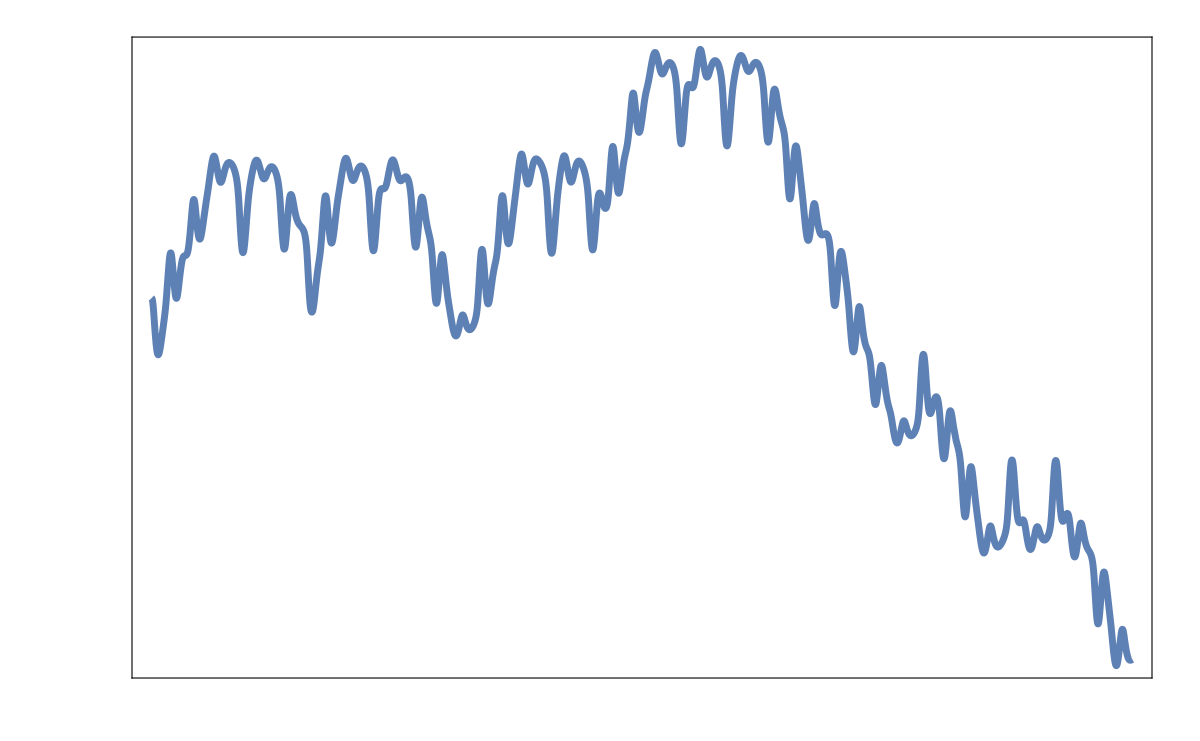

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.05;
T = 200;
ω = 3.5;
sol3 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
FigPlot3 = Plot[(θ[t]/. sol3)/2, {t, 0, T},PlotRange->All,
Axes->False,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-10,5,5}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["535Bonnet.svg", FigPlot3]
```

535Bonnet.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega35d05.csv", data]
```

omega35d05.csv

{{θ[t]→InterpolatingFunction[…][t]}}

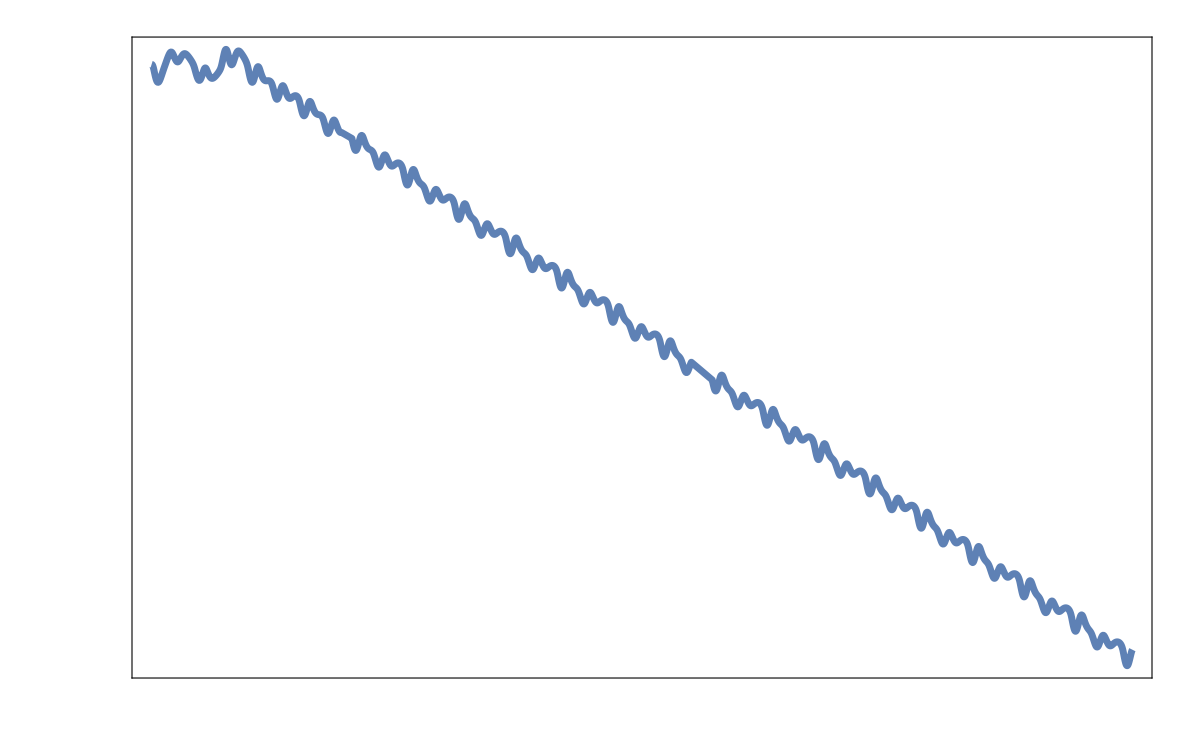

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.05;
T = 200;
ω = 3;
sol4 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
FigPlot4 = Plot[(θ[t]/. sol4)/2, {t, 0, T},PlotRange->All,
Axes->False,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-50,0,10}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["53Bonnet.svg", FigPlot4]
```

53Bonnet.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega3d05.csv", data]
```

omega3d05.csv

Oscillating modes appear as we increase the distance at constant frequency

{{θ[t]→InterpolatingFunction[…][t]}}

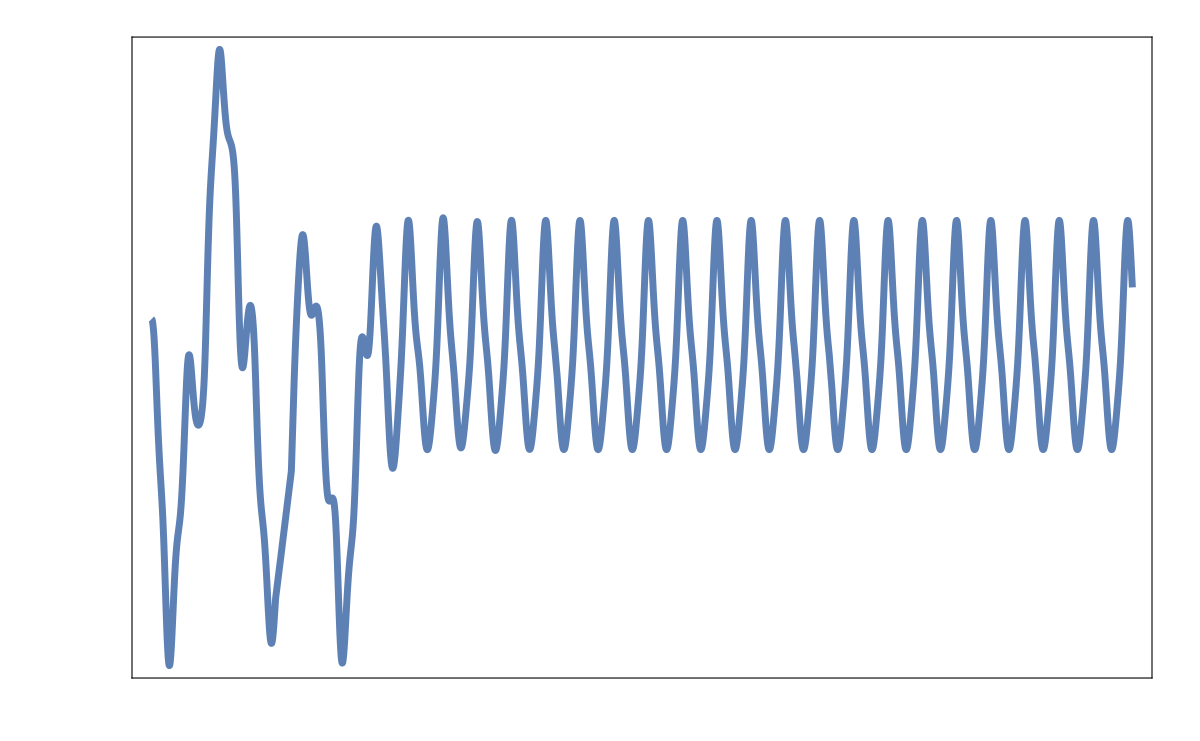

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.10;
T = 200;
ω = 4.5;
sol5 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
SecFigPlot1 = Plot[(θ[t]/. sol5)/2, {t, 0, T},PlotRange->All,
Axes->False,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-3,2,1}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["SecBonnet1.svg", SecFigPlot1]
```

SecBonnet1.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega45d1.csv", data]
```

omega45d1.csv

{{θ[t]→InterpolatingFunction[…][t]}}

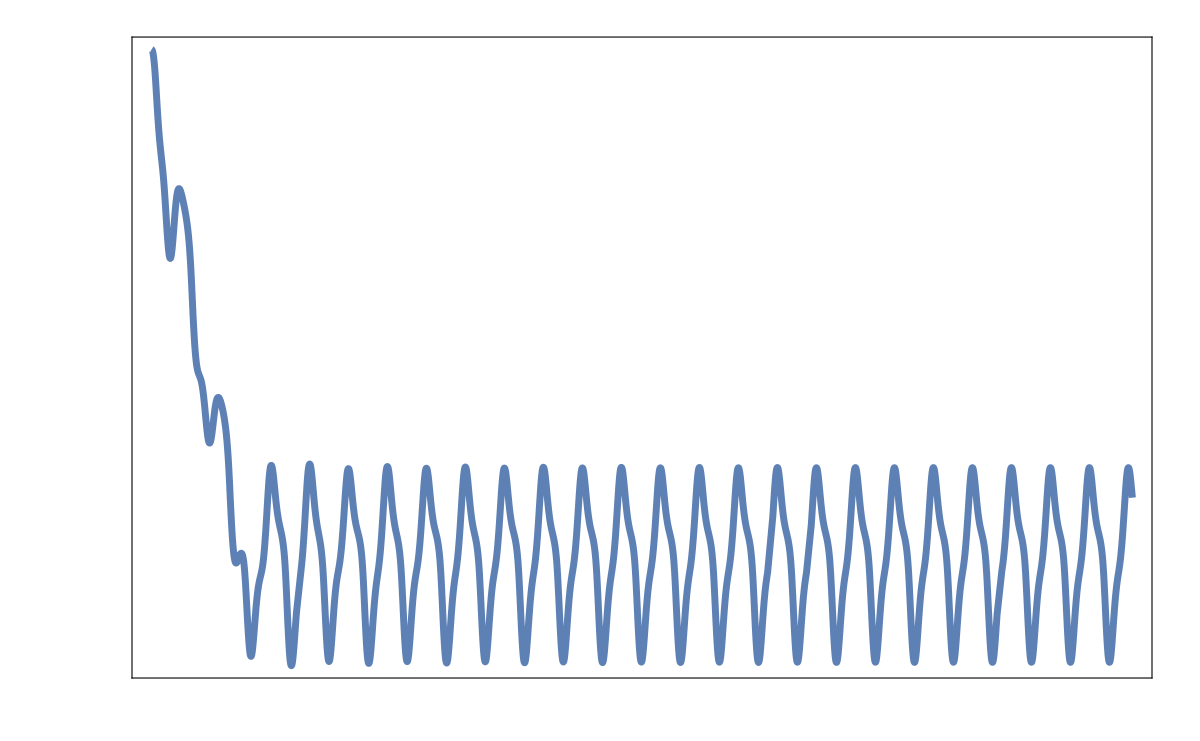

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.10;
T = 200;
ω = 3.95;
sol6 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
SecFigPlot2 = Plot[(θ[t]/. sol6)/2, {t, 0, T},PlotRange->All,
Axes->False,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-10,0,2}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["SecBonnet2.svg", SecFigPlot2]
```

SecBonnet2.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega395d1.csv", data]
```

omega395d1.csv

{{θ[t]→InterpolatingFunction[…][t]}}

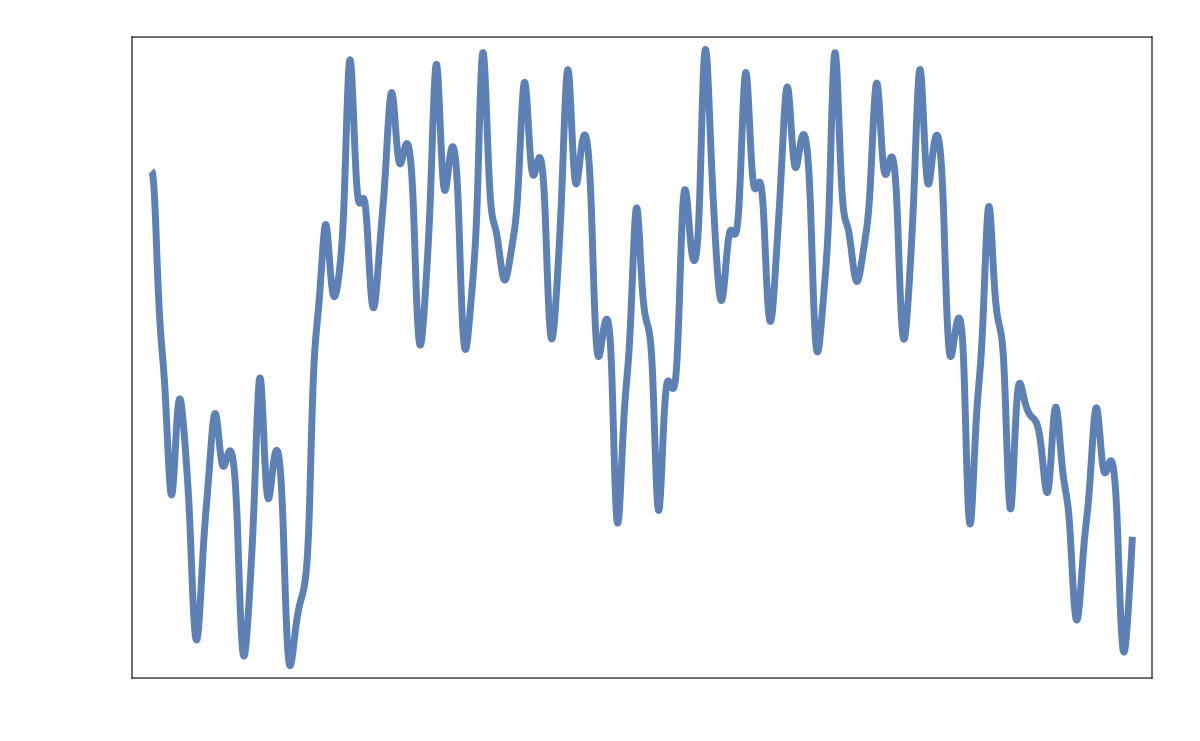

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.10;
T = 200;
ω = 3.5;
sol7 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
SecFigPlot3 = Plot[(θ[t]/. sol7)/2, {t, 0, T},PlotRange->All,
Axes->False,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-5,1,1}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["SecBonnet3.svg", SecFigPlot3]
```

SecBonnet3.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega35d1.csv", data]
```

omega35d1.csv

{{θ[t]→InterpolatingFunction[…][t]}}

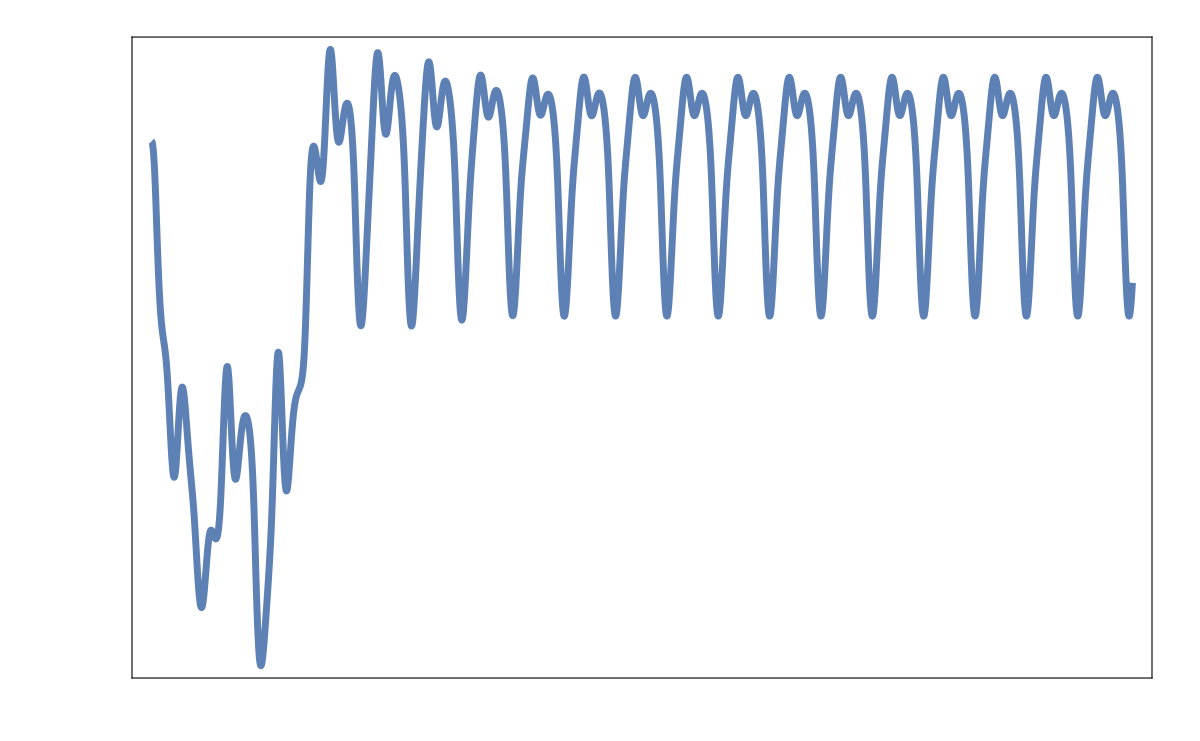

```mathematica
Clear[B,ω0, ω ,A , ϕ,α,d,T]
B =10;
ω0=5;

A = 0.3;

R=0.1;
c = 0.7;
h= 0.01;

ϕ=0;
α=0;
d=0.10;
T = 200;
ω = 3;
sol8 = NDSolve[{eq ==0, θ[0]==0, θ'[0]==0}, θ[t], {t, 0, T}]
SecFigPlot4 = Plot[(θ[t]/. sol8)/2, {t, 0, T},PlotRange->All,
Axes->False,
PlotStyle->AbsoluteThickness[5],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,200,50}],Table[{y,, {0.01, 0}},{y,-5,1,1}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200]
Clear[B,ω0, ω ,A , ϕ,α,d,T]
```

```mathematica
Export["SecBonnet4.svg", SecFigPlot4]
```

SecBonnet4.svg

```mathematica
data=Table[{t,θ[t]/. sol[[1]]},{t,0,200,0.01}];
Export["omega3d1.csv", data]
```

omega3d1.csv

## Linear stability (Mathieu equation)

```mathematica
(*Mathieu coefficients*)
C1[ϕ_, α_, d_]=F[0, ϕ, α, d];
```

```mathematica
C2[ϕ_, α_, d_]=D[F[θ, ϕ, α, d], θ]/.θ->0;
```

```mathematica
f1 = 12  + Sqrt[(10 C2[0, α, d])^2/16 - 1/(2Pi)^2]/(2Pi);
f2 = 12   - Sqrt[(10 C2[0, α, d])^2/16 - 1/(2Pi)^2]/(2Pi);
```

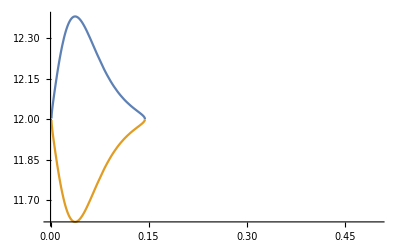

```mathematica
Plot[{ f1/.{R->0.1, h->0.01, c->0.7,α->0}, f2/.{R->0.1, h->0.01, c->0.7, α->0}}, {d, 0, 0.5}]
```

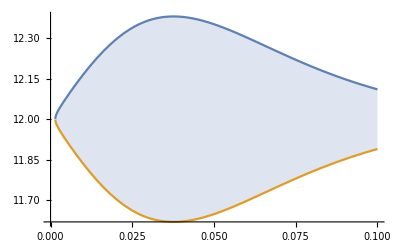
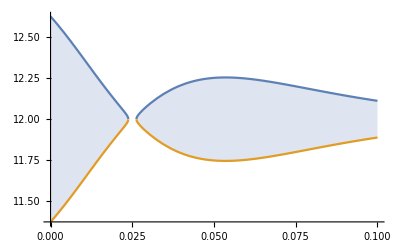
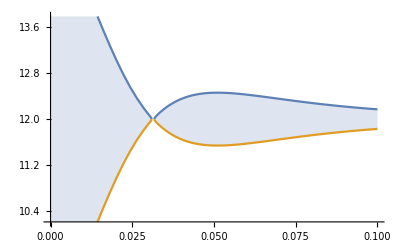
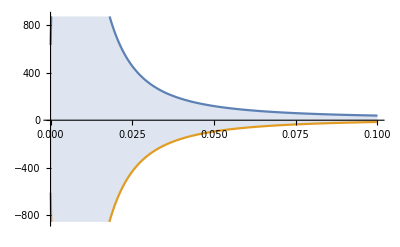
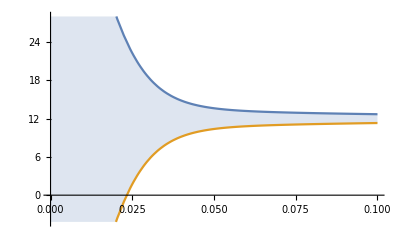
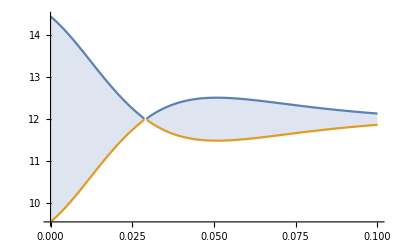
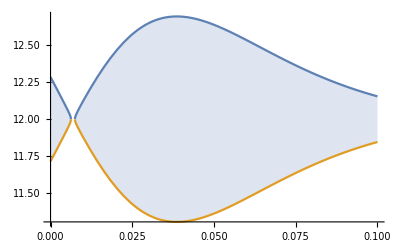
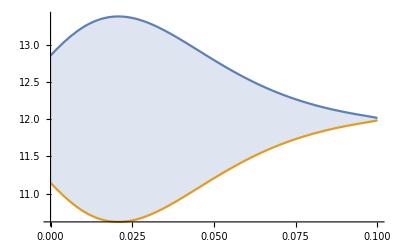

```mathematica
Table[Plot[{ f1/.{R->0.1, h->0.01, c->0.7}, f2/.{R->0.1, h->0.01, c->0.7}}, {d, 0, 0.1},Filling->{1->{2}}],{α, 0,2Pi,0.5}]
```

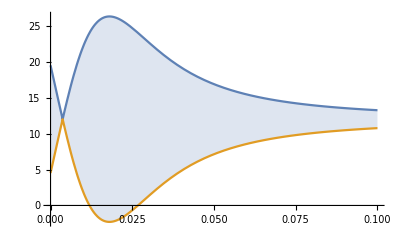
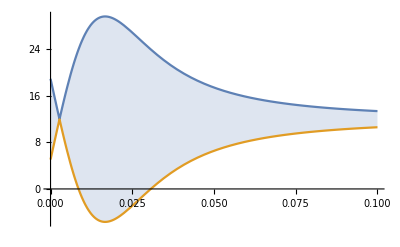
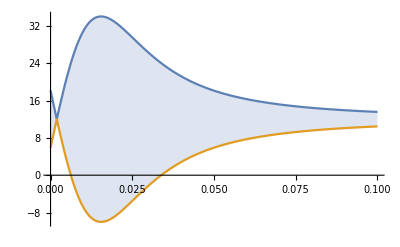
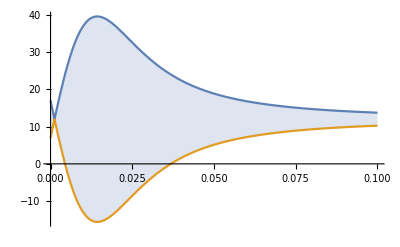
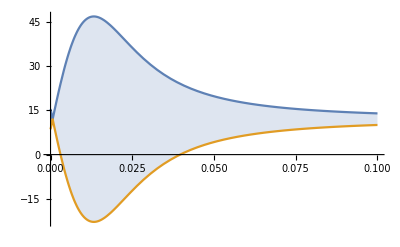
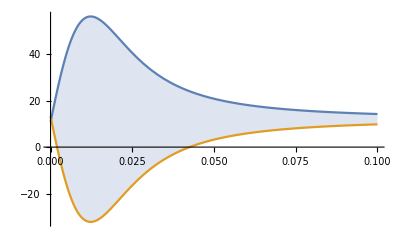
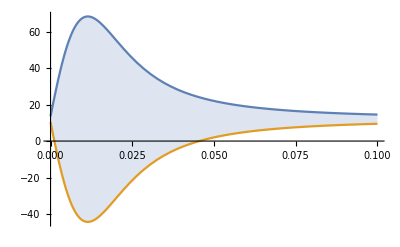
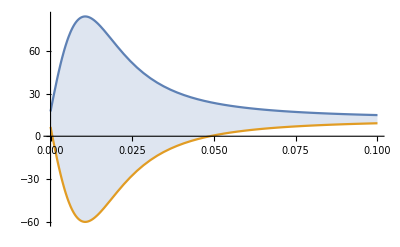

```mathematica
Table[Plot[{ f1/.{R->0.1, h->0.01, c->0.7}, f2/.{R->0.1, h->0.01, c->0.7}}, {d, 0, 0.1},PlotRange->All, Filling->{1->{2}}],{α, 1.3, 1.5, 0.01}]
```

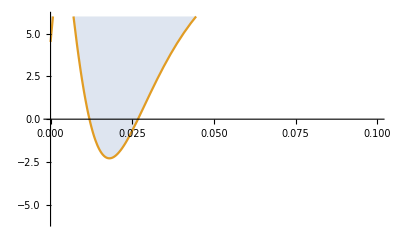
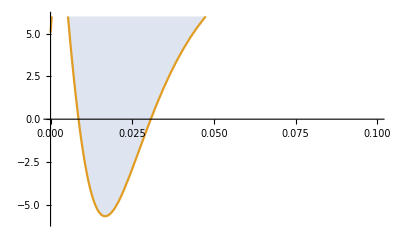
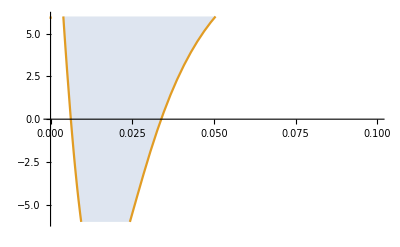
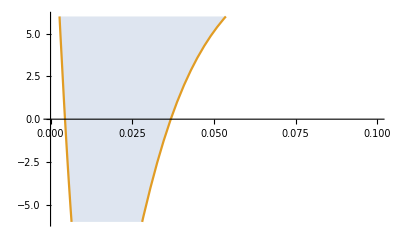
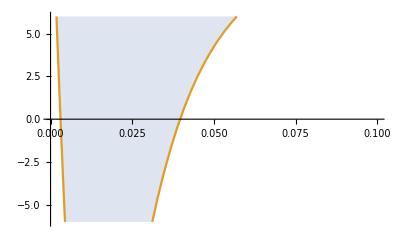
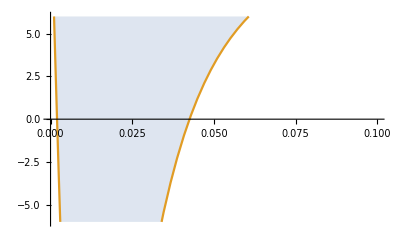
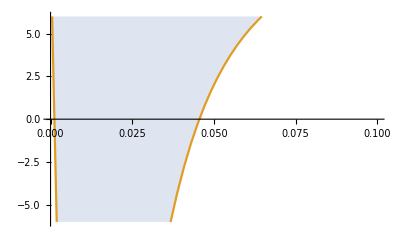
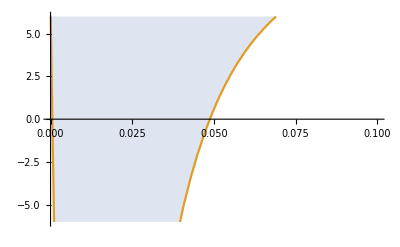
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{ f1/.{R->0.1, h->0.01, c->0.7}, f2/.{R->0.1, h->0.01, c->0.7}}, {d, 0, 0.1},PlotRange->{{0, 0.1}, {-6, 6}}, Filling->{1->{2}}],{α, 1.3, 1.5, 0.01}]
```

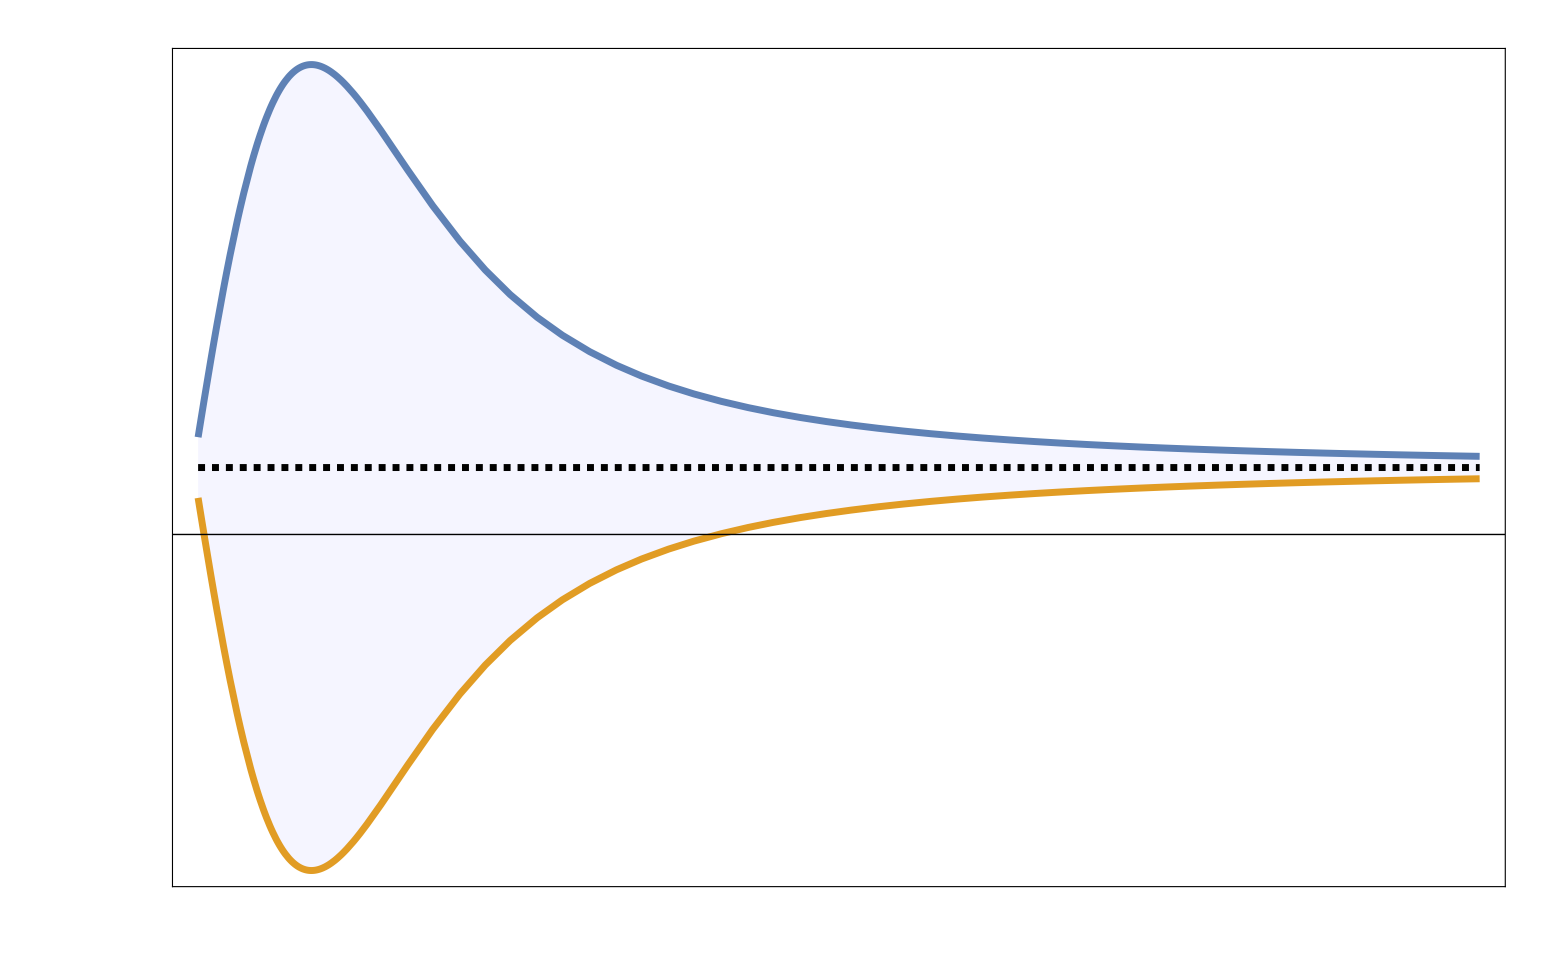

```mathematica
BigFig =Plot[{ f1/.{R->0.1, h->0.01, c->0.7,α->1.37}, f2/.{R->0.1, h->0.01, c->0.7,α->1.37}}, {d, 0, 0.12},
PlotRange->All,
PlotStyle->AbsoluteThickness[5],
Filling->{1->{2}},
FillingStyle->Directive[Blue,Opacity[0.04]],
Frame->True,
Axes->False,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
Epilog->{{AbsoluteThickness[5],Black,Dashed,Line[{{0,12},{0.12,12}}]},{Thick,Black,Line[{{-1,0},{1,0}}]}},
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,0.13,0.02}],Table[{y,, {0.01, 0}},{y,-100,100,20}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1600
]
```

```mathematica
Export["Unstable_region.svg",BigFig]
```

Unstable_region.svg

```mathematica
bluePts={{0.04,1},{0.04,2},{0.04,3},{0.04,4},{0.04,5},{0.04,6}, {0.05,1},{0.05,2},{0.05,3},{0.05,4},{0.05,5},{0.05,6},{0.06,4},{0.06,6}};
greenPts={{0.06,1},{0.06,2},{0.06,3},{0.06,5},  {0.07,1},{0.07,2},{0.07,3},{0.07,4},{0.07,5},{0.07,6}};
r=0.03;
```

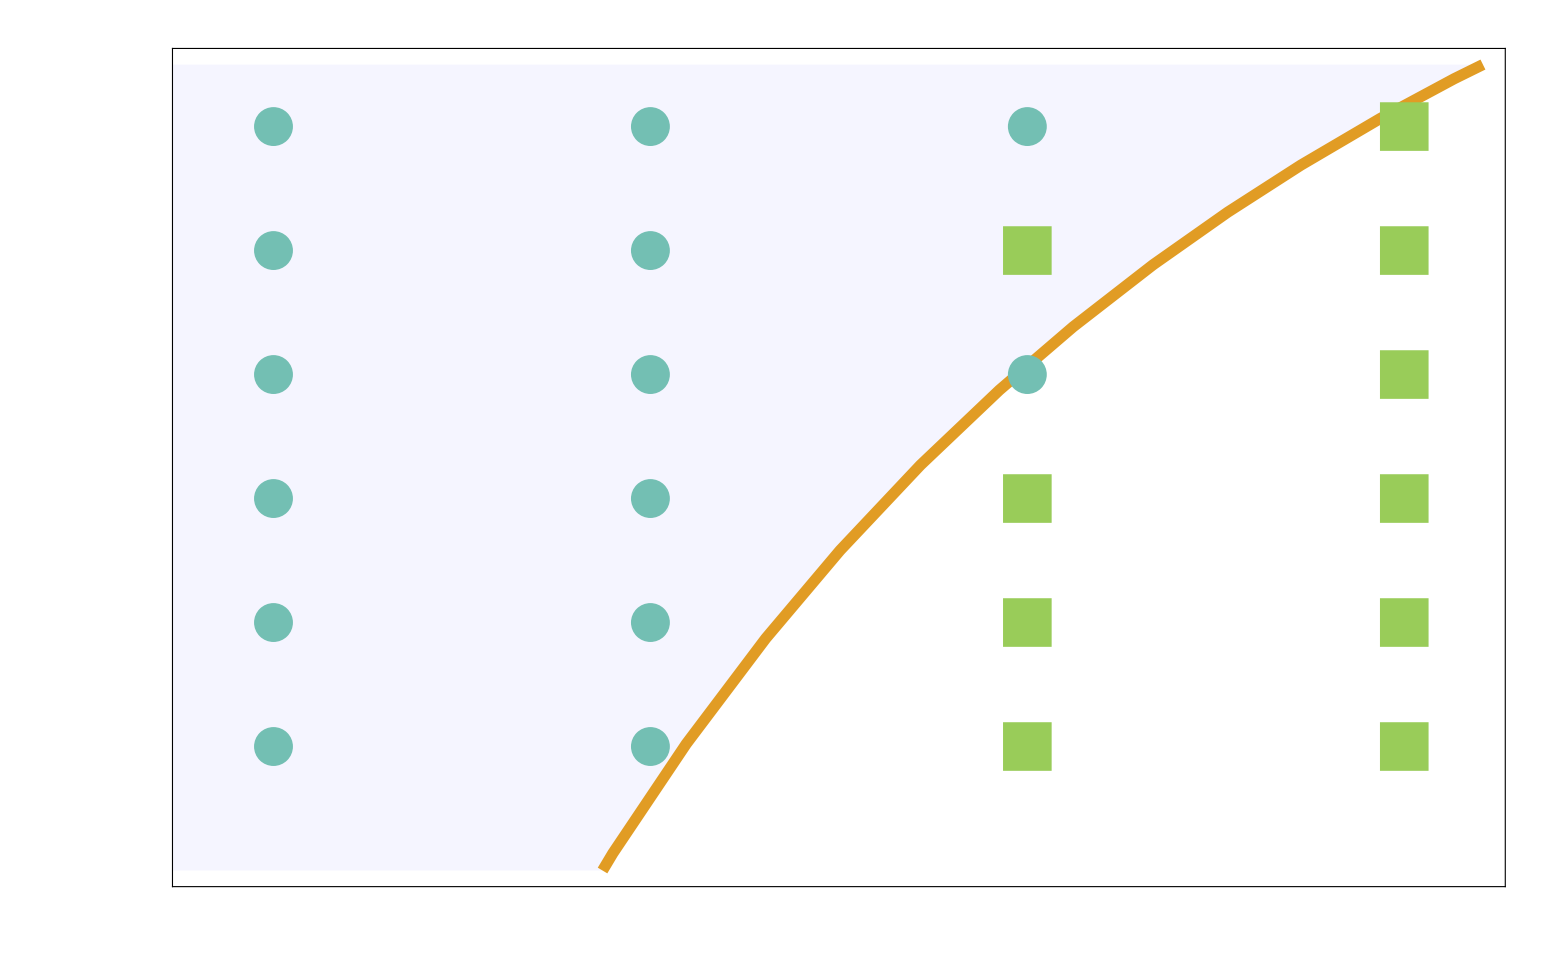

```mathematica
BigFig2 =Show[Plot[{ f1/.{R->0.1, h->0.01, c->0.7,α->1.37}, f2/.{R->0.1, h->0.01, c->0.7,α->1.37}}, {d, 0, 0.1},
PlotRange->{{0.038, 0.072}, {0,6.5}},
PlotStyle->AbsoluteThickness[8],
Filling->{1->{2}},
FillingStyle->Directive[Blue,Opacity[0.04]],
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0.04,0.07,0.01}],Table[{y,, {0.01, 0}},{y,0,6,1}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1600
],
ListPlot[{bluePts,greenPts},PlotStyle->{RGBColor[0.45,0.75,0.70],RGBColor[0.60,0.80,0.35]},PlotMarkers->{{"●",40},(*disk*){"■",50}    (*square*)}]
]
```

```mathematica
Export["Unstable_region_zoom.svg",BigFig2]
```

Unstable_region_zoom.svg